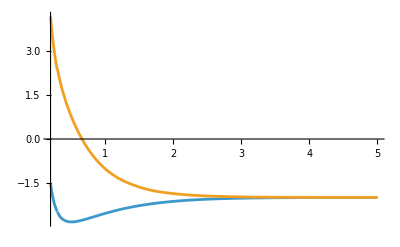

```mathematica
geradeData=Import["/Users/zelimir/Work/Physics-Thesis/thesis-2/ZelimirOverleaf/MathematicaCodeFinal/gerade1sV3.mx"];
geradePotential=Table[{geradeData⟦i,1⟧,geradeData⟦i,3⟧},{i,1,27}];

ungeradeData=Import["/Users/zelimir/Work/Physics-Thesis/thesis-2/ZelimirOverleaf/MathematicaCodeFinal/ungerade1sV3.mx"];
ungeradePotential=Table[{ungeradeData⟦i,1⟧,ungeradeData⟦i,3⟧},{i,1,27}];
long[R_]:=-2.0-0.082/R^4;
geradefun=Interpolation[geradePotential];
ungeradefun=Interpolation[ungeradePotential];

(*Fit to a model*)
gdata=Drop[geradePotential,{5,27}];
udata=Drop[ungeradePotential,{5,27}];
model[R_,C1_,C2_,C3_]:=C1 Exp[-C2 R]/R+C3;

gnlm=NonlinearModelFit[gdata,model[R,C1,C2,C3],{C1,C2,C3},R];
unlm=NonlinearModelFit[udata,model[R,C1,C2,C3],{C1,C2,C3},R];
gshort[R_]:=model[R,C1,C2,C3]/. gnlm["BestFitParameters"];
ushort[R_]:=model[R,C1,C2,C3]/. unlm["BestFitParameters"];
gpot[R_]=Piecewise[{{gshort[R],R≤0.3},{geradefun[R],0.3<R<13.0},{long[R],R≥13.0}}];
upot[R_]=Piecewise[{{ushort[R],R≤0.3},{ungeradefun[R],0.3<R<13.0},{long[R],R≥13.0}}];
Plot[{gpot[R],upot[R]},{R,0.2,5},PlotRange->All]
```

```mathematica
(*e=0.1/27.21;*)μ=1866.0/2.0;
(*k=2 μ e;*)
kB=0.695; (*Boltzman in AU,cm-1K*)
(*λ=2π/k*)
a0=5.29188^-11;
r0=0.01;
rend=100;

(* For a single partial wave m, energy e and distance r, up to rend*)
computePhaseShifts[m_,e_,r0_,rend_] := Module[{k,equG,equU,solsG,solsU,fg,fu, ylogG, ylogU, sl, cl, slp, clp, bG, bU},
k=2 μ e;
equG:=yg''[r]+yg'[r]/r-2 μ (gpot[r]+2) yg[r]-m^2/r^2 yg[r]+2 μ e yg[r];
equU:=yu''[r]+yu'[r]/r-2 μ (upot[r]+2) yu[r]-m^2/r^2 yu[r]+2 μ e yu[r];
solsG=Flatten[NDSolve[{equG==0,yg[r0]==0,yg'[r0]==1},yg,{r,r0,rend},MaxSteps->200000]];
solsU=Flatten[NDSolve[{equU==0,yu[r0]==0,yu'[r0]==1},yu,{r,r0,rend},MaxSteps->200000]];
fg[r_]=yg[r]/. solsG;
fu[r_]=yu[r]/. solsU;
ylogG[r_]:=fg'[r]/fg[r];
ylogU[r_]:=fu'[r]/fu[r];
sl[n_,r_]:=BesselJ[n,k r];
cl[n_,r_]:=HankelH1[n,k r];
slp[n_,r_]:=Derivative[0,1][sl][n,r];
clp[n_,r_]:=Derivative[0,1][cl][n,r];
bG[n_,r_]:=(-I)^(Abs[n]) (slp[n,r]-ylogG[r]×sl[n,r])/(clp[n,r]-ylogG[r]×cl[n,r]);
bU[n_,r_]:=(-I)^(Abs[n]) (slp[n,r]-ylogU[r]×sl[n,r])/(clp[n,r]-ylogU[r]×cl[n,r]);
If[m==0,Return[{Abs[N[bG[m,rend]]],Abs[N[bG[m,rend]-bU[m,rend]]]^2}],
Return[{2 Abs[N[bG[m,rend]]],2 Abs[N[bG[m,rend]-bU[m,rend]]]^2}]]	
];
computePhaseShifts[10,0.003,0.1,100]
```

{0.239731,1.39365}

```mathematica
(*e=collision energy in eV,r0,rend-R range*)
computeCrossSect[eV_,r0_,rend_]:=Module[{phaseShiftForAllm,eH,kk,crossSection},
eH=eV/27.21; (*energy Hartree*)
kk=2 μ eH;
(*m-partial waves*)
phaseShiftForAllm=Table[{m,computePhaseShifts[m,eH,r0,rend]},{m,0,40}];
crossSection=Total[phaseShiftForAllm,{1}]⟦2⟧];
      {eV, crossSection}
;

crossSection=Table[computeCrossSect[e,r0,rend],{e,0.01,1,0.01}];
crossSectionGraphSC=Interpolation[{crossSection⟦All,1⟧,crossSection⟦All,2⟧⟦All,1⟧}//Transpose]
crossSectionGraphCT=Interpolation[{crossSection⟦All,1⟧,crossSection⟦All,2⟧⟦All,2⟧}//Transpose];
```

{eV,crossSection}

Part::partd: Part specification {0.01,0.01,0.01,0.01,0.01,0.01,0.01,0.01,0.01,0.01,0.01,0.01,0.01,0.01,0.01,0.01,0.01,0.01,0.01,0.01,0.01,0.01,0.01,0.01,0.01,0.01,0.01,0.01,0.01,0.01,0.01,0.01,0.01,0.01,0.01,0.01,0.01,0.01,0.01,0.01,0.01,0.01,0.01,0.01,0.01,0.01,0.01,0.01,0.01,0.01,«50»}⟦All,1⟧ is longer than depth of object.

Transpose::nmtx: The first two levels of {{0.01,0.02,0.03,0.04,0.05,0.06,0.07,0.08,0.09,0.1,0.11,0.12,0.13,0.14,0.15,0.16,0.17,0.18,0.19,0.2,0.21,0.22,0.23,0.24,0.25,0.26,0.27,0.28,0.29,0.3,0.31,0.32,0.33,0.34,0.35,0.36,0.37,0.38,0.39,0.4,0.41,0.42,0.43,0.44,0.45,0.46,0.47,0.48,0.49,0.5,«50»},{0.01,«49»,«50»}⟦«1»⟧} cannot be transposed.

Interpolation::innd: First argument in {{0.01,0.02,0.03,0.04,0.05,0.06,0.07,0.08,0.09,0.1,0.11,0.12,«27»,0.4,0.41,0.42,0.43,0.44,0.45,0.46,0.47,0.48,0.49,0.5,«50»},«1»}^T does not contain a list of data and coordinates.

Interpolation[Transpose[{{0.01,0.02,0.03,0.04,0.05,0.06,0.07,0.08,0.09,0.1,0.11,0.12,0.13,0.14,0.15,0.16,0.17,0.18,0.19,0.2,0.21,0.22,0.23,0.24,0.25,0.26,0.27,0.28,0.29,0.3,0.31,0.32,0.33,0.34,0.35,0.36,0.37,0.38,0.39,0.4,0.41,0.42,0.43,0.44,0.45,0.46,0.47,0.48,0.49,0.5,0.51,0.52,0.53,0.54,0.55,0.56,0.57,0.58,0.59,0.6,0.61,0.62,0.63,0.64,0.65,0.66,0.67,0.68,0.69,0.7,0.71,0.72,0.73,0.74,0.75,0.76,0.77,0.78,0.79,0.8,0.81,0.82,0.83,0.84,0.85,0.86,0.87,0.88,0.89,0.9,0.91,0.92,0.93,0.94,0.95,0.96,0.97,0.98,0.99,1.},{0.01,0.01,0.01,0.01,0.01,0.01,0.01,0.01,0.01,0.01,0.01,0.01,0.01,0.01,0.01,0.01,0.01,0.01,0.01,0.01,0.01,0.01,0.01,0.01,0.01,0.01,0.01,0.01,0.01,0.01,0.01,0.01,0.01,0.01,0.01,0.01,0.01,0.01,0.01,0.01,0.01,0.01,0.01,0.01,0.01,0.01,0.01,0.01,0.01,0.01,0.01,0.01,0.01,0.01,0.01,0.01,0.01,0.01,0.01,0.01,0.01,0.01,0.01,0.01,0.01,0.01,0.01,0.01,0.01,0.01,0.01,0.01,0.01,0.01,0.01,0.01,0.01,0.01,0.01,0.01,0.01,0.01,0.01,0.01,0.01,0.01,0.01,0.01,0.01,0.01,0.01,0.01,0.01,0.01,0.01,0.01,0.01,0.01,0.01,0.01}⟦All,1⟧}]]

Part::partd: Part specification {0.01,0.01,0.01,0.01,0.01,0.01,0.01,0.01,0.01,0.01,0.01,0.01,0.01,0.01,0.01,0.01,0.01,0.01,0.01,0.01,0.01,0.01,0.01,0.01,0.01,0.01,0.01,0.01,0.01,0.01,0.01,0.01,0.01,0.01,0.01,0.01,0.01,0.01,0.01,0.01,0.01,0.01,0.01,0.01,0.01,0.01,0.01,0.01,0.01,0.01,«50»}⟦All,2⟧ is longer than depth of object.

Transpose::nmtx: The first two levels of {{0.01,0.02,0.03,0.04,0.05,0.06,0.07,0.08,0.09,0.1,0.11,0.12,0.13,0.14,0.15,0.16,0.17,0.18,0.19,0.2,0.21,0.22,0.23,0.24,0.25,0.26,0.27,0.28,0.29,0.3,0.31,0.32,0.33,0.34,0.35,0.36,0.37,0.38,0.39,0.4,0.41,0.42,0.43,0.44,0.45,0.46,0.47,0.48,0.49,0.5,«50»},{0.01,«49»,«50»}⟦«1»⟧} cannot be transposed.

Interpolation::innd: First argument in {{0.01,0.02,0.03,0.04,0.05,0.06,0.07,0.08,0.09,0.1,0.11,0.12,«27»,0.4,0.41,0.42,0.43,0.44,0.45,0.46,0.47,0.48,0.49,0.5,«50»},«1»}^T does not contain a list of data and coordinates.